## Black Holes, Problem Set 10 SOLUTION

## Problem 1 — Practice with Parametrized Paths

Here is a very cool path, to be considered from ϕ=0 to ϕ=π:       r(ϕ)=(a(1-f^2))/(1-fcosϕ).    In this formula, a and f are just numbers. Let us graph this function with a=5 and f=4/5, in which case it simplifies to:

```mathematica
r[ϕ_]:=9/(5-4Cos[ϕ]);
```

It is of course a continuous function, but we are going to manually make some estimates regarding this function and it is easiest to do that if we make the estimates on a discrete and modest number of segments — let’s make that 6 segments numbered from 0 to 5, and there will be 7 points.

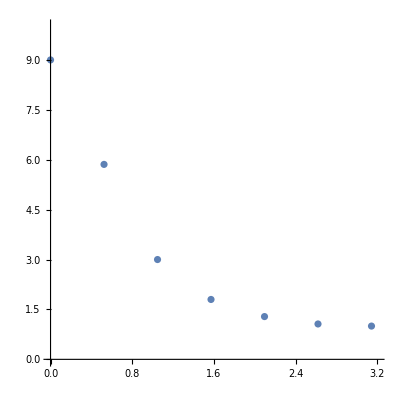

```mathematica
points = Table[{ϕ,r[ϕ]}, {ϕ, 0, Pi, Pi/6}];
ListPlot[points, PlotRange->{{0, 3.2},{0, 10}}, AspectRatio->1]
```

### (a) Tabulate Δϕ for each of the six segments (b) Tabulate r and Δr for each of the eight segments

Now you have some estimates to make and a table to fill in. What should you use for r? Let’s use the average of the r- value of the left and right endpoints of each segment. And for Δr? Just use the difference (which is negative, because this is a decreasing function of ϕ, but in part (c) you will see that only the square of the difference matters). Do your estimates to 1-decimal place accuracy. It won’t matter much if you round odd decimals up or down. Since I had Mathematica at my disposal, I did everything to two decimal places.

```mathematica
TableForm[Table[{Round[r[i Pi / 6],0.01], Round[r[(i+1)Pi / 6],0.01], Round[(r[i*Pi /6] + r[(i+1)Pi / 6])/2,0.01], Round[r[i*Pi /6] - r[(i+1)Pi / 6],0.01], Round[Pi/6, 0.01]}, {i, 0, 5}],TableHeadings->{Range[0, 5], {"r (left),", "r (right)", "r (average)", "Δr", "Δφ"}}]
```

| r (left), | r (right) | r (average) | Δr | Δφ
0 | 9. | 5.86 | 7.43 | 3.14 | 0.52
1 | 5.86 | 3. | 4.43 | 2.86 | 0.52
2 | 3. | 1.8 | 2.4 | 1.2 | 0.52
3 | 1.8 | 1.29 | 1.54 | 0.51 | 0.52
4 | 1.29 | 1.06 | 1.17 | 0.22 | 0.52
5 | 1.06 | 1. | 1.03 | 0.06 | 0.52

### (c) Tabulate the lengths of the line segments (d) Sum the values of Δs

Use  this metric (and now you see why I had you tabulate the average value of r in addition to the difference Δr): Δs=√((Δr)^2+(r^2(Δϕ))^2).

```mathematica
lengths=Table[{
Round[Sqrt[
(Round[(r[i*Pi /6] + r[(i+1)Pi / 6])/2,0.01])^2 Round[Pi/6,0.01]^2+ (Round[r[i*Pi /6] - r[(i+1)Pi / 6],0.01])^2
],0.01]
}, {i, 0, 5}];TableForm[lengths,TableHeadings->{Range[0, 6], {"     Δs    "}}]
Total[Flatten[lengths]]
```

|      Δs    
0 | 4.98
1 | 3.67
2 | 1.73
3 | 0.95
4 | 0.65
5 | 0.54

12.52

### (e) Interpretation and cross-check

The metric I had you use is actually the metric of spherical polar coordinates with θ=π/2 and Δθ=0.

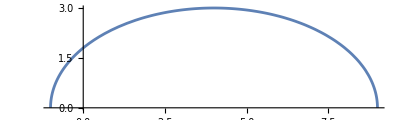

```mathematica
PolarPlot[r[ϕ], {ϕ,0,Pi}, AspectRatio->3/10]
```

This is half of an ellipse, which is why I said this is a “very cool” path — at least Newton would have thought so. What is the length of half of an ellipse? Well, I’ll tell you, in this case it is π √((3^2+5^2)/2)

```mathematica
Round[Pi Sqrt[17],0.01]
```

12.95

## Problem 2 — Set Up the Construction Problem

Your classmates (Sasha and Eden), are going to do the full consultation to the Black Hole Construction Company. The other 6 of you have heard about the consulting project but are only going to do Part A. Please do Part A by making two drawings that show (i) What the President mistakenly had his robots doing, and (ii) what his robots should instead be doing.

If you make your drawings appropriate for building shells from 11,000 meters down to 10,000 meters in 1-meter intervals that would be very hard to draw to scale. Therefore change the problem to be to build shells extending from 15km down to 10km in 1km intervals. That should be drawable to scale. Of course, spacetime is curved and you have flat paper. So you will either have to sacrifice the r scale or the circumferences. Let’s make the circumferences realistic, and sacrifice the r scale. In Part A, you are only being asked to draw one such pair of shells.

To do this really well, I need a bunch of numbers. Note that 2M=10km. Building shells at 10km, 11km, ..., 15km is building them at 1.0*2M, 1.1*2M, 1.2*2M, 1.3*2M, 1.4*2M, and 1.5*2M. The scale factor 1/(√(1-(2M)/r)) for the first shell can be estimated by putting 1.05*2M into this formula, and we get √(1-(2M)/(1.05*2M))=√(1-1/1.05)=0.2! Egadz. We haven’t built the first wall 1km of reduced radius away, we have built it 0.2km of reduced radius away. Now we build the next wall, and a good estimate of the scale factor is now half way from 1.02 to 1.12 or 1.07 and √(1-1/1.07) is close to 0.3 so the next wall is 0.3km of reduced radius away. A good estimate of the next scale factor is half way from 1.05 to 1.15 or 1.1 and √(1-1/1.10) is almost exactly 0.3. So the next wall is again 0.3km away. For the next scale factor, we use √(1-1/1.13) is a little more than 0.3. The next scale factor is almost 0.4, etc.